# Test for VScaling

## Start

```mathematica
(* Add to path packages *)
packageDirectory=FileNameJoin[{NotebookDirectory[],"1DPackage","*"}];
$Path=Join[$Path,FileNames[packageDirectory]];
```

```mathematica
<<"ReadSintel`"
<<"pyramid1d`"
```

```mathematica
(* Declare path for SINTEL Data depending on user*)
baseSINTEL=Switch[$UserName,
"fieri","D:\\MastersMathematica\\Data\\Sintel",
"roys","/home/roys/datasets/SINTEL-stereo"
];
```

## Data

```mathematica
(* downscaling *)
r=2;
{ia,ib,id,io}=read[baseSINTEL,"bamboo_1","0001",r,"clean"];

(* {1,44},{1,102} arbitrary size to make the method faster *)
nx=170/r;
ny=300/r;
{ia,ib,id,io}=ImageTake[#,{ny,ny+44},{nx,nx+102}]&/@{ia,ib,id,io}
ImageDimensions[#]&/@{ia,ib,id,io}

max=MinMax[Flatten[ImageData[id]]][[2]];
Print["max dv=", max]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{{103,45},{103,45},{103,45},{103,45}}

max dv=12.5952

## Test

#### Little Functions

```mathematica
pyrfi[ia_,ib_,row_,lvlmax_]:=Block[{pyrfia,pyrfib},
pyrfia=pyrFuncGen[ImageData[ia][[row]], lvlmax];
pyrfib=pyrFuncGen[ImageData[ib][[row]],lvlmax];

Flatten[{pyrfia,pyrfib},{{2},{1},{3}}]
]
```

```mathematica
row=20;
lvlmin=1;
lvlmax=5;

pyrfiab=pyrfi[ia,ib,row,lvlmax];
```

#### View Functions

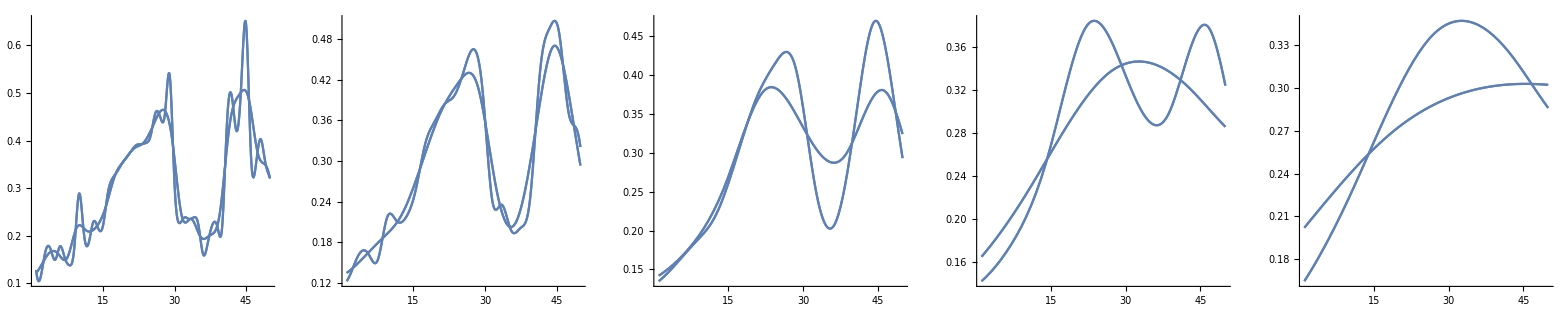

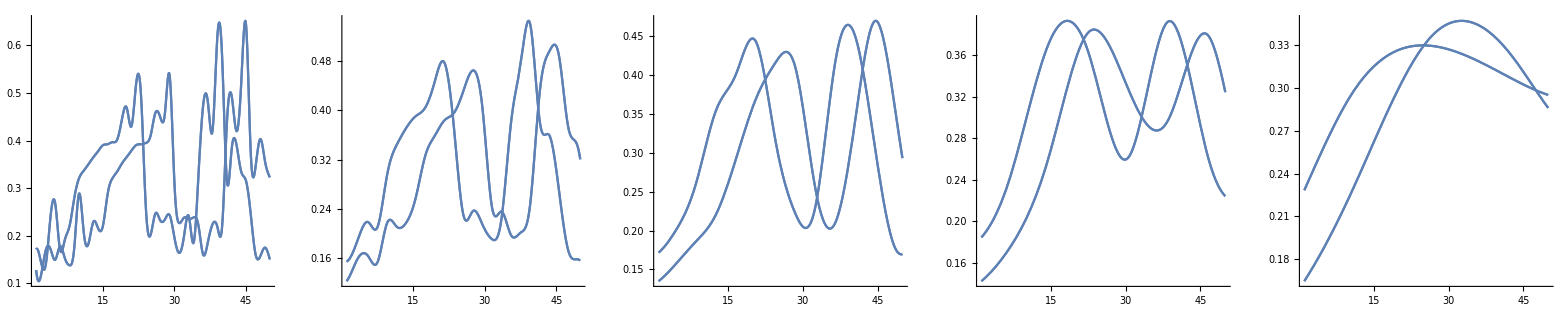

```mathematica
g0=GraphicsRow[Table[
Plot[{#[x],#[x]}&/@pyrfiab[[i;;i+1,1,1]],{x,1,50}]
,{i,1,lvlmax}]];

g1=GraphicsRow[Table[
Plot[{#[x],#[x]}&/@pyrfiab[[i,All,1]],{x,1,50}]
,{i,1,lvlmax}]];

Show[g0, ImageSize->Scaled[1]]
Show[g1, ImageSize->Scaled[1]]
```

#### V equations through scales

```mathematica
Cp[p_,lvl_]:=(pyrfiab[[lvl,1,1]][p]+pyrfiab[[lvl,2,1]][p])/2;
I1t[p_,lvl_]:=pyrfiab[[lvl,1,1]][p]-Cp[p,lvl];
I2t[p_,lvl_]:=Cp[p,lvl]-pyrfiab[[lvl,2,1]][p];
```

```mathematica
I1t[10,1]
```

-0.0161792

```mathematica
I1x[p_,lvl_]:=pyrfiab[[lvl,1,2]][p]+Sign[pyrfiab[[lvl,1,2]][p]]*0.5*pyrfiab[[lvl,1,2]]'[p];
I2x[p_,lvl_]:=pyrfiab[[lvl,2,2]][p]+Sign[pyrfiab[[lvl,2,2]][p]]*0.5*pyrfiab[[lvl,2,2]]'[p];
```

```mathematica
I1x[10,1]
```

-0.174615

```mathematica
Fv[p_,lvl_]:=(I1t[p,lvl]/I1x[p,lvl])+(I2t[p,lvl]/I2x[p,lvl])
```

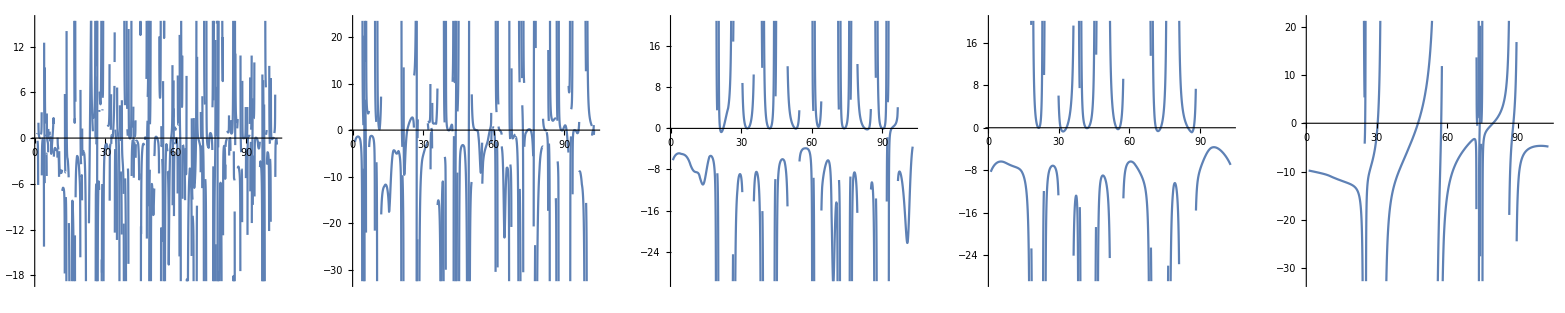

```mathematica
g1=GraphicsRow[Table[
Plot[Fv[p,lvl],{p,1,103}]
,{lvl,1,lvlmax}]];
Show[g1, ImageSize->Scaled[1]]
```

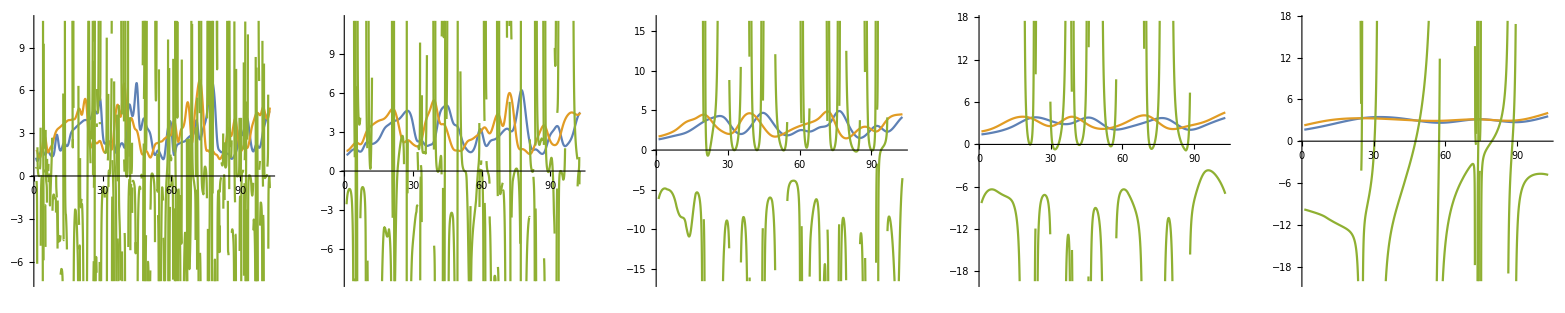

```mathematica
g2=GraphicsRow[Table[
Plot[{pyrfiab[[lvl,1,1]][p]*10,pyrfiab[[lvl,2,1]][p]*10,Fv[p,lvl]},{p,1,103}]
,{lvl,1,lvlmax}]];
Show[g2, ImageSize->Scaled[1]]
```